# variable bending field

```mathematica
Mdrift={{1,ldr},{0,1}}; MatrixForm[Mdrift]
```

(1 | ldr
0 | 1)

```mathematica
Mqx={{1,0},{-1/f,1}}; MatrixForm[Mqx]
```

(1 | 0
-1/f | 1)

```mathematica
Mqy=Mqx/.f->-f; MatrixForm[Mqy]
```

(1 | 0
1/f | 1)

```mathematica
Mdipx={{1,s},{0,1}};MatrixForm[Mdipx]
```

(1 | s
0 | 1)

```mathematica
Mdipy={{1,s},{0,1}};MatrixForm[Mdipy]
```

(1 | s
0 | 1)

```mathematica
Mbend={{1,s,θ̃},{0,1,θ},{0,0,1}};MatrixForm[Mbend]
```

(1 | s | θ̃
0 | 1 | θ
0 | 0 | 1)

at the center of the dipole

```mathematica
Mbend1=Mbend/.s->Ld;MatrixForm[Mbend1]
```

(1 | Ld | θ̃
0 | 1 | θ
0 | 0 | 1)

## -Graphics-

from s(symmetry point) till ld/2(the center of the dipole)

```mathematica
Mx=Simplify[(Mdrift/.ldr->s3).(Mqx/.f->f2).(Mdrift/.ldr->s2).(Mqx/.f->f1).(Mdrift/.ldr->s1).(Mdipx/.s->Ld)]; MatrixForm[Mx]
```

((f1 (f2-s3)+s2 s3-f2 (s2+s3))/(f1 f2) | (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))/(f1 f2)
-(f1+f2-s2)/(f1 f2) | (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2))/(f1 f2))

```mathematica
My=Simplify[(Mdrift/.ldr->s3).(Mqy/.f->f2).(Mdrift/.ldr->s2).(Mqy/.f->f1).(Mdrift/.ldr->s1).(Mdipy/.s->Ld)]; MatrixForm[My]
```

((s2 s3+f1 (f2+s3)+f2 (s2+s3))/(f1 f2) | ((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))/(f1 f2)
(f1+f2+s2)/(f1 f2) | ((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2))/(f1 f2))

from ld/2 till ld/2,that means for the whole cell
Mcell=M’M

```mathematica
Mx'=Simplify[Mx/.{Mx[[2,2]]->Mx[[1,1]],Mx[[1,1]]->Mx[[2,2]]}]; MatrixForm[Mx']
```

((-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2))/(f1 f2) | (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))/(f1 f2)
-(f1+f2-s2)/(f1 f2) | (f1 (f2-s3)+s2 s3-f2 (s2+s3))/(f1 f2))

```mathematica
Mcellx=FullSimplify[Mx'.Mx];MatrixForm[Mcellx]
```

((f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)/(f1^2 f2^2) | (2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))))/(f1^2 f2^2)
-(2 (f1+f2-s2) (f1 (f2-s3)+s2 s3-f2 (s2+s3)))/(f1^2 f2^2) | (f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)/(f1^2 f2^2))

```mathematica
My'=Simplify[My/.{My[[2,2]]->My[[1,1]],My[[1,1]]->My[[2,2]]}]; MatrixForm[My']
```

(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2))/(f1 f2) | ((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))/(f1 f2)
(f1+f2+s2)/(f1 f2) | (s2 s3+f1 (f2+s3)+f2 (s2+s3))/(f1 f2))

```mathematica
Mcelly=FullSimplify[My'.My];MatrixForm[Mcelly]
```

((((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2) | (2 ((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2)
(2 (f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3))/(f1^2 f2^2) | (((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2))

dispersion for x from the symmetry point(s) till the center of the dipole

```mathematica
Msx=Simplify[(Mdrift/.ldr->s3).(Mqx/.f->f2).(Mdrift/.ldr->s2).(Mqx/.f->f1).(Mdrift/.ldr->s1)];MatrixForm[Msx]
```

((f1 (f2-s3)+s2 s3-f2 (s2+s3))/(f1 f2) | (-s1 (-s2 s3+f2 (s2+s3))+f1 (-(s1+s2) s3+f2 (s1+s2+s3)))/(f1 f2)
-(f1+f2-s2)/(f1 f2) | (f1 (f2-s1-s2)+s1 (-f2+s2))/(f1 f2))

```mathematica
Dsx={{Msx[[1,1]],Msx[[1,2]],0},{Msx[[2,1]],Msx[[2,2]],0},{0,0,1}};MatrixForm[FullSimplify[Dsx]]
```

((f1 (f2-s3)+s2 s3-f2 (s2+s3))/(f1 f2) | (-s1 (-s2 s3+f2 (s2+s3))+f1 (-(s1+s2) s3+f2 (s1+s2+s3)))/(f1 f2) | 0
-(f1+f2-s2)/(f1 f2) | (f1 (f2-s1-s2)+s1 (-f2+s2))/(f1 f2) | 0
0 | 0 | 1)

```mathematica
Disp=Dsx.Mbend1;MatrixForm[FullSimplify[Disp]]
```

((f1 (f2-s3)+s2 s3-f2 (s2+s3))/(f1 f2) | (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))/(f1 f2) | ((-s1 (-s2 s3+f2 (s2+s3))+f1 (-(s1+s2) s3+f2 (s1+s2+s3))) θ-(-s2 s3+f1 (-f2+s3)+f2 (s2+s3)) θ̃)/(f1 f2)
-(f1+f2-s2)/(f1 f2) | (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2))/(f1 f2) | ((f1 (f2-s1-s2)+s1 (-f2+s2)) θ-(f1+f2-s2) θ̃)/(f1 f2)
0 | 0 | 1)

finding the twiss transform matrix

```mathematica
Twissx={{Mx[[1,1]]^2,-2 Mx[[1,1]] Mx[[1,2]],Mx[[1,2]]^2},{-Mx[[1,1]] Mx[[2,1]], Mx[[1,1]] Mx[[2,2]]+Mx[[1,2]] Mx[[2,1]], -Mx[[1,2]] Mx[[2,2]]},{Mx[[2,1]]^2,-2 Mx[[2,1]] Mx[[2,2]],Mx[[2,2]]^2}};MatrixForm[FullSimplify[Twissx]]
```

((f1 (f2-s3)+s2 s3-f2 (s2+s3))^2/(f1^2 f2^2) | -(2 (f1 (f2-s3)+s2 s3-f2 (s2+s3)) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))))/(f1^2 f2^2) | (-f1 f2 (Ld+s1+s2)+f1 (-f2+Ld+s1+s2) s3+(Ld+s1) (-s2 s3+f2 (s2+s3)))^2/(f1^2 f2^2)
((f1+f2-s2) (f1 (f2-s3)+s2 s3-f2 (s2+s3)))/(f1^2 f2^2) | (f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)/(f1^2 f2^2) | -((-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))))/(f1^2 f2^2)
(f1+f2-s2)^2/(f1^2 f2^2) | (2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2))/(f1^2 f2^2) | ((Ld+s1) (f2-s2)+f1 (-f2+Ld+s1+s2))^2/(f1^2 f2^2))

```mathematica
Twissy={{My[[1,1]]^2,-2 My[[1,1]] My[[1,2]],My[[1,2]]^2},{-My[[1,1]] My[[2,1]], My[[1,1]] My[[2,2]]+My[[1,2]] My[[2,1]], -My[[1,2]] My[[2,2]]},{My[[2,1]]^2,-2 My[[2,1]] My[[2,2]],My[[2,2]]^2}};MatrixForm[FullSimplify[Twissy]]
```

((f2 (f1+s2)+(f1+f2+s2) s3)^2/(f1^2 f2^2) | -(2 (f2 (f1+s2)+(f1+f2+s2) s3) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2) | (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3)))^2/(f1^2 f2^2)
-((f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3))/(f1^2 f2^2) | (((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2) | -(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(f1^2 f2^2)
(f1+f2+s2)^2/(f1^2 f2^2) | -(2 (f1+f2+s2) ((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)))/(f1^2 f2^2) | ((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2))^2/(f1^2 f2^2))

Optics calculations

cosϕ=(TrMcell)/2

```mathematica
cosϕx=Simplify[(Mcellx[[1,1]]+Mcellx[[2,2]])/2]
```

1/(f1^2 f2^2)(f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)

```mathematica
cosϕy=Simplify[(Mcelly[[1,1]]+Mcelly[[2,2]])/2]
```

1/(f1^2 f2^2)(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))

sinϕ = (1 - cos^2 ϕ)^(1/2)

```mathematica
sinϕx= Simplify[(1 - (cosϕx)^2)^(1/2)]
```

√(1-1/(f1^4 f2^4)(f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)^2)

```mathematica
sinϕy= Simplify[(1 - (cosϕy)^2)^(1/2)]
```

√(1-1/(f1^4 f2^4)(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))^2)

by the matrix Mcellx[[1,2]]= βsinϕ where β at the center of the dipole

```mathematica
sinϕxm=Simplify[Mcellx[[1,2]]/βxcd]
```

1/(f1^2 f2^2 βxcd)2 (0.0246055+f2 (-0.0821091-1. Ld)+f1 (-0.381777+f2-1. Ld)+0.299668 Ld) ((0.0246055+f1 (-0.381777-1. Ld)+0.299668 Ld) s3+f2 (-0.0246055-0.299668 Ld-0.0821091 s3-1. Ld s3+f1 (0.381777+Ld+s3)))

```mathematica
sinϕym=Simplify[Mcelly[[1,2]]/βycd]
```

1/(f1^2 f2^2 βycd)2 (0.0246055+0.299668 Ld+f2 (0.0821091+Ld)+f1 (0.381777+f2+Ld)) ((0.0246055+0.299668 Ld+f1 (0.381777+Ld)) s3+f2 (0.0246055+0.0821091 s3+Ld (0.299668+s3)+f1 (0.381777+Ld+s3)))

```mathematica
Solve[sinϕx==sinϕxm,βxcd]
```

```mathematica
Solve[sinϕy==sinϕym,βycd]
```

finding βsx,αsx,γsx,ηsx,ηsx’ by using Twiss matrices and as initial conditions βxcd,αxcd,γxcd,ηxcd,ηxcd’

```mathematica
{βsx,αsx,γsx}=Simplify[Twissx.{βxcd,αxcd,γxcd}]
```

{1/(f1^2 f2^2)(-2 (f1 (f2-s3)+s2 s3-f2 (s2+s3)) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))) αxcd+(f1 (f2-s3)+s2 s3-f2 (s2+s3))^2 βxcd+((Ld+s1) (-s2 s3+f2 (s2+s3))-f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))^2 γxcd),1/(f1^2 f2^2)(((-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1 (f2-s3)+s2 s3-f2 (s2+s3))-(f1+f2-s2) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))) αxcd+(f1+f2-s2) (f1 (f2-s3)+s2 s3-f2 (s2+s3)) βxcd-(-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (-(Ld+s1) (-s2 s3+f2 (s2+s3))+f1 (-(Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))) γxcd),1/(f1^2 f2^2)(2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) αxcd+(f1+f2-s2)^2 βxcd+((Ld+s1) (f2-s2)+f1 (-f2+Ld+s1+s2))^2 γxcd)}

```mathematica
{βsy,αsy,γsy}=Simplify[Twissy.{βycd,αycd,γycd}]
```

{1/(f1^2 f2^2)(-2 (s2 s3+f1 (f2+s3)+f2 (s2+s3)) ((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))) αycd+(s2 s3+f1 (f2+s3)+f2 (s2+s3))^2 βycd+((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))^2 γycd),1/(f1^2 f2^2)((((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (s2 s3+f1 (f2+s3)+f2 (s2+s3))+(f1+f2+s2) ((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3)))) αycd-(f1+f2+s2) (s2 s3+f1 (f2+s3)+f2 (s2+s3)) βycd-((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) ((Ld+s1) (s2 s3+f2 (s2+s3))+f1 ((Ld+s1+s2) s3+f2 (Ld+s1+s2+s3))) γycd),1/(f1^2 f2^2)(-2 (f1+f2+s2) ((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) αycd+(f1+f2+s2)^2 βycd+((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2))^2 γycd)}

```mathematica
{ηsx,ηsxx,one}=Simplify[Disp.{ηxcd,ηxcdd,1}]
```

{1/(f1 f2)(-(-s2 s3+f2 (s2+s3)) (ηxcd+Ld ηxcdd+s1 (ηxcdd+θ))+f1 (-s3 (ηxcd+Ld ηxcdd+(s1+s2) (ηxcdd+θ))+f2 (ηxcd+Ld ηxcdd+(s1+s2+s3) (ηxcdd+θ)))-(-s2 s3+f1 (-f2+s3)+f2 (s2+s3)) θ̃),-1/(f1 f2)(f1 (ηxcd+Ld ηxcdd+s1 ηxcdd+s2 ηxcdd+s1 θ+s2 θ-f2 (ηxcdd+θ))+(f2-s2) (ηxcd+Ld ηxcdd+s1 (ηxcdd+θ))+(f1+f2-s2) θ̃),1}

introducing conditions at the center of the dipole

```mathematica
TMEx=FullSimplify[{βsx,αsx,γsx,ηsx,ηsxx}/.{γxcd->(1+αxcd^2)/βxcd}/.{αxcd->0,ηxcdd->0}]
```

{((-f1 f2 (Ld+s1+s2)+f1 (-f2+Ld+s1+s2) s3+(Ld+s1) (-s2 s3+f2 (s2+s3)))^2/βxcd+(f1 (f2-s3)+s2 s3-f2 (s2+s3))^2 βxcd)/(f1^2 f2^2),1/(f1^2 f2^2)(-1/βxcd((Ld+s1) (f2-s2)+f1 (-f2+Ld+s1+s2)) (-f1 f2 (Ld+s1+s2)+f1 (-f2+Ld+s1+s2) s3+(Ld+s1) (-s2 s3+f2 (s2+s3)))+(f1+f2-s2) (f1 (f2-s3)+s2 s3-f2 (s2+s3)) βxcd),(((Ld+s1) (f2-s2)+f1 (-f2+Ld+s1+s2))^2/βxcd+(f1+f2-s2)^2 βxcd)/(f1^2 f2^2),1/(f1 f2)(-(-s2 s3+f2 (s2+s3)) (ηxcd+s1 θ)+f1 (-s3 (ηxcd+(s1+s2) θ)+f2 (ηxcd+(s1+s2+s3) θ))-(-s2 s3+f1 (-f2+s3)+f2 (s2+s3)) θ̃),-((f2-s2) (ηxcd+s1 θ)+f1 (ηxcd+(-f2+s1+s2) θ)+(f1+f2-s2) θ̃)/(f1 f2)}

```mathematica
TMEy=FullSimplify[{βsy,αsy,γsy}/.{γycd->(1+αycd^2)/βycd}/.αycd->0]
```

{((f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3)))^2/βycd+(f2 (f1+s2)+(f1+f2+s2) s3)^2 βycd)/(f1^2 f2^2),-1/(f1^2 f2^2)(1/βycd((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3)))+(f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3) βycd),(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2))^2/βycd+(f1+f2+s2)^2 βycd)/(f1^2 f2^2)}

```mathematica
f12=Simplify[Solve[{TMEx[[4]]==ηss,TMEx[[5]]==0},{f1,f2}]]
```

{{f1→(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃),f2→-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)}}

```mathematica
{fq1,fq2}=Simplify[Flatten[{f1/.f12,f2/.f12}]]/.ηxcd->ηr ηmin/.ηmin->-I3/(2I4)
```

{(s2 (-(I3 ηr)/(2 I4)+s1 θ+θ̃))/(-(I3 ηr)/(2 I4)-ηss+s1 θ+s2 θ+θ̃),-(s2 ηss)/(-(I3 ηr)/(2 I4)-ηss+s1 θ+θ̃)}

```mathematica
{{f1->(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃),f2->-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)}}
```

{{f1→(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃),f2→-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)}}

```mathematica
hs=FullSimplify[(2 s3 (ηxcd+s1 θ+θ̃))/(-s2+(√(4 s3 (ηxcd+s1 θ) (-(Ld+s1) ηxcd+(Ld (Ld+s1)+βxcd^2) θ)+s2^2 (ηxcd^2-2 Ld ηxcd θ+(Ld^2+βxcd^2) θ^2)+θ̃ (-8 (Ld+s1) s3 ηxcd+4 s3 (Ld^2-s1^2+βxcd^2) θ+2 s2^2 (ηxcd-Ld θ)+(s2^2-4 (Ld+s1) s3) θ̃)))/(√(ηxcd^2-2 Ld ηxcd θ+(Ld^2+βxcd^2) θ^2+θ̃ (2 ηxcd-2 Ld θ+θ̃))))/.βxcd->3.048206607197994*^8 (1.439145006978807*^-10 ϵr-0.0002501411296362615 √(-5.923520805654349*^-13+3.310083100326479*^-13 ϵr^2-0.002748974888447813 (-5.112179286104773*^-7+0.0006872437221119533 Subscript[η, 0]) Subscript[η, 0]))/.Subscript[η, 0]->ηxcd/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.f1->ef1/.f2->ef2/.ϵr->2]
```

0.0459375+0.000197232 ⅈ

```mathematica
ef1=FullSimplify[(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)/.ηss->0.0510/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100]
```

10.5604

```mathematica
ef2=FullSimplify[-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)/.ηss->0.0510/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100]
```

-0.677784

```mathematica
cosfpsi=FullSimplify[1/(f1^2 f2^2)(((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) (f2 (f1+s2)+(f1+f2+s2) s3)+(f1+f2+s2) (f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.f1->ef1/.f2->ef2]
```

-1.16261

```mathematica
cosx=FullSimplify[1/(f1^2 f2^2)(f2 (2 (Ld+s1) (f2-s2) s2+f1^2 (f2-2 (Ld+s1+s2))-2 f1 (f2 (Ld+s1+s2)-s2 (2 (Ld+s1)+s2)))-2 (-(Ld+s1) (f2-s2)+f1 (f2-Ld-s1-s2)) (f1+f2-s2) s3)/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.f1->ef1/.f2->ef2]
```

5.22988

```mathematica
betaycd=FullSimplify[(-√((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) √(f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(√(-(f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3)))/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.f1->ef1/.f2->ef2]
```

0.-0.26237 ⅈ

```mathematica
βqx1/.βxcd->3.048206607197994*^8 (1.439145006978807*^-10 ϵr-0.0002501411296362615 √(-5.923520805654349*^-13+3.310083100326479*^-13 ϵr^2-0.002748974888447813 (-5.112179286104773*^-7+0.0006872437221119533 Subscript[η, 0]) Subscript[η, 0]))/.Subscript[η, 0]->ηxcd/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0404990,θ̃->(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0,θ->-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)}/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.f1->ef1/.f2->ef2/.ϵr->2
```

βqx1

```mathematica
βqy1/.βycd->betaycd/.Subscript[η, 0]->ηxcd/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0006510,θ̃->(L0^2 (λ^2+(-1+λ)^2 ρ))/(λ^2 ρ0),θ->(L0 (λ+ρ-λ ρ))/(λ ρ0)}/.Ld->L0/λ/.L0->-(θ ρ0 λ)/(2 (-λ-ρ+λ ρ))/.θ->2Pi/100/.λ->0.38008/.ρ->0.3/.ρ0->5.4/.f1->ef1/.f2->ef2/.ϵr->2
```

βqy1

```mathematica
βqx2/.βxcd->96896.94311247382 (3.4926634021582205*^-7 ϵr-0.5615923939542538 √(-8.226321361827077*^-13+3.86786255105754*^-13 ϵr^2-0.003021023718742156 (-6.601862472643262*^-7+0.000755255929685539 Subscript[η, 0]) Subscript[η, 0]))/.Subscript[η, 0]->ηxcd/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0006510,θ̃->(L0^2 (λ^2+(-1+λ)^2 ρ))/(λ^2 ρ0),θ->(L0 (λ+ρ-λ ρ))/(λ ρ0)}/.Ld->L0/λ/.L0->-(θ ρ0 λ)/(2 (-λ-ρ+λ ρ))/.θ->2Pi/100/.λ->0.38008/.ρ->0.3/.ρ0->5.4/.f1->ef1/.f2->ef2/.ϵr->2
```

βqx2

```mathematica
βqy2/.βycd->betaycd/.Subscript[η, 0]->ηxcd/.{s2->0.9,s1->0.9,s3->0.5,ηxcd->0.0006510,θ̃->(L0^2 (λ^2+(-1+λ)^2 ρ))/(λ^2 ρ0),θ->(L0 (λ+ρ-λ ρ))/(λ ρ0)}/.Ld->L0/λ/.L0->-(θ ρ0 λ)/(2 (-λ-ρ+λ ρ))/.θ->2Pi/100/.λ->0.38008/.ρ->0.3/.ρ0->5.4/.f1->ef1/.f2->ef2/.ϵr->2
```

βqy2

```mathematica
αssx=FullSimplify[TMEx[[2]]/.{f1->fq1,f2->fq2},{βxcd>0,s1>0,s2>0,s3>0}]
```

1/(4 βxcd ηss^2)(1/I4^2(-I3^2 s3 ηr^2+2 I3 I4 ηr (s2 ηss-2 Ld s3 θ)+4 I4^2 (-(Ld+s1) ηss^2+(2 Ld+s1) s2 ηss θ-s3 (Ld^2+βxcd^2) θ^2))+((4 I3 s3 ηr)/I4-4 s2 ηss+8 Ld s3 θ) θ̃-4 s3 (θ̃)^2+(8 I4 ((Ld+s1)^2+βxcd^2) ηss θ (ηss-s2 θ))/(-I3 ηr+2 I4 s1 θ+2 I4 θ̃))

```mathematica
αssy=Simplify[TMEy[[2]]/.{f1->(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃),f2->-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)}]
```

-((-ηss+ηxcd+s1 θ+θ̃)^2 (-ηss+ηxcd+s1 θ+s2 θ+θ̃)^2 (1/βycds2 ((Ld+s1) (s2-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃))+(s2 (ηxcd+s1 θ+θ̃) (Ld+s1+s2-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)) (-(s2 (Ld+s1+s2) ηss (ηxcd+s1 θ+θ̃))/((-ηss+ηxcd+s1 θ+θ̃) (-ηss+ηxcd+s1 θ+s2 θ+θ̃))+(s3 (ηxcd+s1 θ+θ̃) (Ld+s1+s2-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)+(Ld+s1) (s3-((s2+s3) ηss)/(-ηss+ηxcd+s1 θ+θ̃)))+βycd (s2-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)+(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)) (-(s2 ηss (s2+(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)))/(-ηss+ηxcd+s1 θ+θ̃)+s3 (s2-(s2 ηss)/(-ηss+ηxcd+s1 θ+θ̃)+(s2 (ηxcd+s1 θ+θ̃))/(-ηss+ηxcd+s1 θ+s2 θ+θ̃)))))/(s2^4 ηss^2 (ηxcd+s1 θ+θ̃)^2)

```mathematica
{ηs1,ηs2}=FullSimplify[ηss/.Solve[αssx==0,ηss]]
```

{(I3^2 I4 s2 ηr^2+4 I3 I4^2 s2 ηr (Ld θ-θ̃)+4 I4^3 s2 ((Ld^2+βxcd^2) θ^2-2 Ld θ θ̃+(θ̃)^2)-√(I4^2 (I3^2 ηr^2+4 I3 I4 Ld ηr θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3 ηr-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3) ηr^2+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) ηr θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (I3 (-s2^2+4 (Ld+s1) s3) ηr+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(4 I4^2 (I3 (Ld+s1) ηr+2 I4 (Ld (Ld+s1)+βxcd^2) θ-2 I4 (Ld+s1) θ̃)),(I3^2 I4 s2 ηr^2+4 I3 I4^2 s2 ηr (Ld θ-θ̃)+4 I4^3 s2 ((Ld^2+βxcd^2) θ^2-2 Ld θ θ̃+(θ̃)^2)+√(I4^2 (I3^2 ηr^2+4 I3 I4 Ld ηr θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3 ηr-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3) ηr^2+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) ηr θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (I3 (-s2^2+4 (Ld+s1) s3) ηr+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(4 I4^2 (I3 (Ld+s1) ηr+2 I4 (Ld (Ld+s1)+βxcd^2) θ-2 I4 (Ld+s1) θ̃))}

```mathematica
{βycd1,βycd2}=FullSimplify[βycd/.Solve[TMEy[[2]]==0,βycd]]
```

{-(√((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) √(f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(√(-(f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3))),(√((Ld+s1) (f2+s2)+f1 (f2+Ld+s1+s2)) √(f1 f2 (Ld+s1+s2)+f1 (f2+Ld+s1+s2) s3+(Ld+s1) (s2 s3+f2 (s2+s3))))/(√(-(f1+f2+s2) (f2 (f1+s2)+(f1+f2+s2) s3)))}

```mathematica
{f11,f22}={FullSimplify[fq1/.ηss->ηs2/.ηxcd->ηr ηmin/.ηmin->-I3/2I4],FullSimplify[fq2/.ηss->ηs2/.ηxcd->ηr ηmin/.ηmin->-I3/2I4]}
```

{(s2 (-(I3 ηr)/(2 I4)+s1 θ+θ̃))/(-(I3 ηr)/(2 I4)+s1 θ+s2 θ+θ̃-(I3^2 I4 s2 ηr^2+4 I3 I4^2 s2 ηr (Ld θ-θ̃)+4 I4^3 s2 ((Ld^2+βxcd^2) θ^2-2 Ld θ θ̃+(θ̃)^2)+√(I4^2 (I3^2 ηr^2+4 I3 I4 Ld ηr θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3 ηr-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3) ηr^2+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) ηr θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (I3 (-s2^2+4 (Ld+s1) s3) ηr+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(4 I4^2 (I3 (Ld+s1) ηr+2 I4 (Ld (Ld+s1)+βxcd^2) θ-2 I4 (Ld+s1) θ̃))),1/(1/s2+1/(2 s3)-(√(I4^2 (I3^2 ηr^2+4 I3 I4 Ld ηr θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3 ηr-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3) ηr^2+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) ηr θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (I3 (-s2^2+4 (Ld+s1) s3) ηr+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(2 I4 s2 s3 (I3^2 ηr^2+4 I3 I4 Ld ηr θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3 ηr-2 I4 Ld θ+I4 θ̃))))}

```mathematica
{f1min,f2min}={FullSimplify[f11/.{ηr->1,βr->1}],FullSimplify[f22/.{ηr->1,βr->1}]}
```

{(s2 (-I3/(2 I4)+s1 θ+θ̃))/(-I3/(2 I4)+s1 θ+s2 θ+θ̃-(I3^2 I4 s2+4 I3 I4^2 s2 (Ld θ-θ̃)+4 I4^3 s2 ((Ld^2+βxcd^2) θ^2-2 Ld θ θ̃+(θ̃)^2)+√(I4^2 (I3^2+4 I3 I4 Ld θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3)+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (-I3 s2^2+4 I3 (Ld+s1) s3+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(4 I4^2 (I3 (Ld+s1)+2 I4 (Ld (Ld+s1)+βxcd^2) θ-2 I4 (Ld+s1) θ̃))),1/(1/s2+1/(2 s3)-(√(I4^2 (I3^2+4 I3 I4 Ld θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3-2 I4 Ld θ+I4 θ̃)) (I3^2 (s2^2-4 (Ld+s1) s3)+4 I3 I4 (Ld s2^2-2 Ld^2 s3+2 s3 (s1-βxcd) (s1+βxcd)) θ+4 I4^2 (Ld (Ld s2^2+4 s1 (Ld+s1) s3)+(s2^2+4 s1 s3) βxcd^2) θ^2+4 I4 θ̃ (-I3 s2^2+4 I3 (Ld+s1) s3+2 I4 (-Ld s2^2+2 Ld^2 s3-2 s1^2 s3+2 s3 βxcd^2) θ+I4 (s2^2-4 (Ld+s1) s3) θ̃))))/(2 I4 s2 s3 (I3^2+4 I3 I4 Ld θ+4 I4^2 (Ld^2+βxcd^2) θ^2+4 I4 θ̃ (-I3-2 I4 Ld θ+I4 θ̃))))}

```mathematica
A={Subscript[cosϕx, TME],cosϕxr}={Simplify[cosϕx/.{f1->fq1,f2->fq2}/.ηss->ηs2/.{ηxcd->ηr ηmin,βxcd->βr βmin}/.{ηmin->-I3/2I4,βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)}/.{ηr->1,βr->1}],Simplify[cosϕx/.{f1->fq1,f2->fq2}/.ηss->ηs2/.{ηxcd->ηr ηmin,βxcd->βr βmin}/.{ηmin->-I3/2I4,βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)}]}
```

{(2 I4 (I4 (I3^2-4 I2 I4) θ^2+I1 (I3+2 I4 Ld θ)^2-4 I1 I4 (I3+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) (I1 I3^2 I4 s2^2-2 I1 I3^2 I4 Ld s3-2 I1 I3^2 I4 s1 s3+4 I1 I3 I4^2 Ld s2^2 θ+I3^3 I4 s3 θ-4 I2 I3 I4^2 s3 θ-4 I1 I3 I4^2 Ld^2 s3 θ+4 I1 I3 I4^2 s1^2 s3 θ-I3^2 I4^2 s2^2 θ^2+4 I2 I4^3 s2^2 θ^2+4 I1 I4^3 Ld^2 s2^2 θ^2-2 I3^2 I4^2 s1 s3 θ^2+8 I2 I4^3 s1 s3 θ^2+8 I1 I4^3 Ld^2 s1 s3 θ^2+8 I1 I4^3 Ld s1^2 s3 θ^2-4 I1 I3 I4^2 s2^2 θ̃+8 I1 I3 I4^2 Ld s3 θ̃+8 I1 I3 I4^2 s1 s3 θ̃-8 I1 I4^3 Ld s2^2 θ θ̃-2 I3^2 I4^2 s3 θ θ̃+8 I2 I4^3 s3 θ θ̃+8 I1 I4^3 Ld^2 s3 θ θ̃-8 I1 I4^3 s1^2 s3 θ θ̃+4 I1 I4^3 s2^2 (θ̃)^2-8 I1 I4^3 Ld s3 (θ̃)^2-8 I1 I4^3 s1 s3 (θ̃)^2+I1 s2 √(1/I1^2I4^2 (I4 (-I3^2+4 I2 I4) θ^2+I1 (I3+2 I4 Ld θ)^2-4 I1 I4 (I3+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) ((I3^2-4 I2 I4) θ (2 I3 s3-I4 (s2^2+4 s1 s3) θ)+I1 (I3+2 I4 Ld θ) (I3 (s2^2-4 (Ld+s1) s3)+2 I4 (4 s1^2 s3+Ld (s2^2+4 s1 s3)) θ)-4 I4 ((I3^2-4 I2 I4) s3 θ+I1 (I3 (s2^2-4 (Ld+s1) s3)+2 I4 (Ld s2^2-2 Ld^2 s3+2 s1^2 s3) θ)) θ̃+4 I1 I4^2 (s2^2-4 (Ld+s1) s3) (θ̃)^2))))/(I1 I3^2 I4 s2+4 I1 I3 I4^2 Ld s2 θ-I3^2 I4^2 s2 θ^2+4 I2 I4^3 s2 θ^2+4 I1 I4^3 Ld^2 s2 θ^2-4 I1 I3 I4^2 s2 θ̃-8 I1 I4^3 Ld s2 θ θ̃+4 I1 I4^3 s2 (θ̃)^2+I1 √(1/I1^2I4^2 (I4 (-I3^2+4 I2 I4) θ^2+I1 (I3+2 I4 Ld θ)^2-4 I1 I4 (I3+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) ((I3^2-4 I2 I4) θ (2 I3 s3-I4 (s2^2+4 s1 s3) θ)+I1 (I3+2 I4 Ld θ) (I3 (s2^2-4 (Ld+s1) s3)+2 I4 (4 s1^2 s3+Ld (s2^2+4 s1 s3)) θ)-4 I4 ((I3^2-4 I2 I4) s3 θ+I1 (I3 (s2^2-4 (Ld+s1) s3)+2 I4 (Ld s2^2-2 Ld^2 s3+2 s1^2 s3) θ)) θ̃+4 I1 I4^2 (s2^2-4 (Ld+s1) s3) (θ̃)^2)))^2,(2 I4 (I4 (I3^2-4 I2 I4) βr^2 θ^2+I1 (I3 ηr+2 I4 Ld θ)^2-4 I1 I4 (I3 ηr+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) (I1 I3^2 I4 s2^2 ηr^2-2 I1 I3^2 I4 Ld s3 ηr^2-2 I1 I3^2 I4 s1 s3 ηr^2+4 I1 I3 I4^2 Ld s2^2 ηr θ-4 I1 I3 I4^2 Ld^2 s3 ηr θ+4 I1 I3 I4^2 s1^2 s3 ηr θ+I3^3 I4 s3 βr^2 ηr θ-4 I2 I3 I4^2 s3 βr^2 ηr θ+4 I1 I4^3 Ld^2 s2^2 θ^2+8 I1 I4^3 Ld^2 s1 s3 θ^2+8 I1 I4^3 Ld s1^2 s3 θ^2-I3^2 I4^2 s2^2 βr^2 θ^2+4 I2 I4^3 s2^2 βr^2 θ^2-2 I3^2 I4^2 s1 s3 βr^2 θ^2+8 I2 I4^3 s1 s3 βr^2 θ^2-4 I1 I3 I4^2 s2^2 ηr θ̃+8 I1 I3 I4^2 Ld s3 ηr θ̃+8 I1 I3 I4^2 s1 s3 ηr θ̃-8 I1 I4^3 Ld s2^2 θ θ̃+8 I1 I4^3 Ld^2 s3 θ θ̃-8 I1 I4^3 s1^2 s3 θ θ̃-2 I3^2 I4^2 s3 βr^2 θ θ̃+8 I2 I4^3 s3 βr^2 θ θ̃+4 I1 I4^3 s2^2 (θ̃)^2-8 I1 I4^3 Ld s3 (θ̃)^2-8 I1 I4^3 s1 s3 (θ̃)^2+I1 s2 √(1/I1^2I4^2 (I4 (-I3^2+4 I2 I4) βr^2 θ^2+I1 (I3 ηr+2 I4 Ld θ)^2-4 I1 I4 (I3 ηr+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) ((I3^2-4 I2 I4) βr^2 θ (2 I3 s3 ηr-I4 (s2^2+4 s1 s3) θ)+I1 (I3 ηr+2 I4 Ld θ) (I3 (s2^2-4 (Ld+s1) s3) ηr+2 I4 (4 s1^2 s3+Ld (s2^2+4 s1 s3)) θ)-4 I4 ((I3^2-4 I2 I4) s3 βr^2 θ+I1 (I3 (s2^2-4 (Ld+s1) s3) ηr+2 I4 (Ld s2^2-2 Ld^2 s3+2 s1^2 s3) θ)) θ̃+4 I1 I4^2 (s2^2-4 (Ld+s1) s3) (θ̃)^2))))/(I1 I3^2 I4 s2 ηr^2+4 I1 I3 I4^2 Ld s2 ηr θ+4 I1 I4^3 Ld^2 s2 θ^2-I3^2 I4^2 s2 βr^2 θ^2+4 I2 I4^3 s2 βr^2 θ^2-4 I1 I3 I4^2 s2 ηr θ̃-8 I1 I4^3 Ld s2 θ θ̃+4 I1 I4^3 s2 (θ̃)^2+I1 √(1/I1^2I4^2 (I4 (-I3^2+4 I2 I4) βr^2 θ^2+I1 (I3 ηr+2 I4 Ld θ)^2-4 I1 I4 (I3 ηr+2 I4 Ld θ) θ̃+4 I1 I4^2 (θ̃)^2) ((I3^2-4 I2 I4) βr^2 θ (2 I3 s3 ηr-I4 (s2^2+4 s1 s3) θ)+I1 (I3 ηr+2 I4 Ld θ) (I3 (s2^2-4 (Ld+s1) s3) ηr+2 I4 (4 s1^2 s3+Ld (s2^2+4 s1 s3)) θ)-4 I4 ((I3^2-4 I2 I4) s3 βr^2 θ+I1 (I3 (s2^2-4 (Ld+s1) s3) ηr+2 I4 (Ld s2^2-2 Ld^2 s3+2 s1^2 s3) θ)) θ̃+4 I1 I4^2 (s2^2-4 (Ld+s1) s3) (θ̃)^2)))^2}

## emit. calc.

```mathematica
ρ1=ρ0
```

ρ0

```mathematica
ρ2=Simplify[ρ0(1+(((s/L0)-1)(r-1)/(L-1)))]
```

(1+((-1+r) (-1+s/L0))/(-1+L)) ρ0

```mathematica
Subscript[ϵ, xNEW]=G (Subscript[β, 0] I1+(1/Subscript[β, 0])(I2+Subscript[η, 0] I3+Subscript[η, 0]^2 I4))
```

G (I1 β_0+(I2+I3 η_0+I4 η_0^2)/β_0)

```mathematica
Subscript[ϵ, xmin]=FullSimplify[Subscript[ϵ, xNEW]/.Subscript[β, 0]->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)/.Subscript[η, 0]->-I3/(2 I4)]
```

(G √I1 √(-I3^2+4 I2 I4))/(√I4)

```mathematica
ϵr*Subscript[ϵ, xmin]
```

(G √I1 √(-I3^2+4 I2 I4) ϵr)/(√I4)

```mathematica
{β01,β02}=FullSimplify[Solve[(G √I1 √(-I3^2+4 I2 I4) ϵr)/(√I4)==G (I1 Subscript[β, 0]+(I2+I3 Subscript[η, 0]+I4 Subscript[η, 0]^2)/Subscript[β, 0]),Subscript[β, 0]]]
```

{{β_0→(√I1 √(-I3^2+4 I2 I4) ϵr+√(-I1 (4 I2 I4+(I3^2-4 I2 I4) ϵr^2+4 I4 η_0 (I3+I4 η_0))))/(2 I1 √I4)},{β_0→(√I1 √(-I3^2+4 I2 I4) ϵr-√(-I1 (4 I2 I4+(I3^2-4 I2 I4) ϵr^2+4 I4 η_0 (I3+I4 η_0))))/(2 I1 √I4)}}

```mathematica
βr1=Simplify[(Subscript[β, 0]/.β01)/βmin/.Subscript[η, 0]->ηr ηmin/.{βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4),ηmin->-I3/(2 I4)}]
```

ϵr+(√(I1 (4 I2 I4 (-1+ϵr^2)-I3^2 (ϵr^2+(-2+ηr) ηr))))/(√I1 √(-I3^2+4 I2 I4))

```mathematica
βr2=Simplify[(Subscript[β, 0]/.β02)/βmin/.Subscript[η, 0]->ηr ηmin/.{βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4),ηmin->-I3/(2 I4)}]
```

ϵr-(√(I1 (4 I2 I4 (-1+ϵr^2)-I3^2 (ϵr^2+(-2+ηr) ηr))))/(√I1 √(-I3^2+4 I2 I4))

```mathematica
FullSimplify[Solve[(Subscript[β, 0]/.β01)==(√(-I3^2+4 I2 I4))/(2 √I1 √I4)ϵr,Subscript[η, 0] ]]
```

{{η_0→-(I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)},{η_0→(-I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)}}

```mathematica
FullSimplify[Solve[(Subscript[β, 0]/.β02)==(√(-I3^2+4 I2 I4))/(2 √I1 √I4)ϵr,Subscript[η, 0] ]]
```

{{η_0→-(I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)},{η_0→(-I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)}}

```mathematica
{η01,η02}={-(I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2),(-I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)}
```

{-(I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2),(-I3 I4+√(I4^2 (-I3^2+4 I2 I4) (-1+ϵr^2)))/(2 I4^2)}

```mathematica
ηr1=Simplify[(η01/ηmin)/.ηmin->-I3/(2 I4)]
```

1+(√(-I4^2 (I3^2-4 I2 I4) (-1+ϵr^2)))/(I3 I4)

```mathematica
Simplify[(η02/ηmin)/.ηmin->-I3/(2 I4)]
```

1-(√(-I4^2 (I3^2-4 I2 I4) (-1+ϵr^2)))/(I3 I4)

```mathematica
FullSimplify[1/(12 ρ0^5)L0^3 (4-(3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/(-1+r)^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ]
```

(L0^3 (4-(3 (-1+λ)^3 ρ^3 (-1+ρ^2-2 Log[L0 (-1+1/λ)] (1+Log[L0 (-1+1/λ)])+2 ρ^2 Log[-(L0 (-1+λ))/(λ ρ)] (1+Log[-(L0 (-1+λ))/(λ ρ)])))/(λ^3 (-1+ρ)^3)))/(12 ρ0^5)

```mathematica
FullSimplify[1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ]
```

1/(20 ρ0^5)L0^5 (1-1/(λ^5 (-1+ρ)^5)5 (-1+λ)^3 ρ^3 (-(λ-ρ) (-1+ρ) (-5 λ+11 (-1+λ) ρ+5 ρ^2)+2 (2 λ (1-4 ρ) ρ+3 ρ^2+λ^2 (-3+2 ρ (2+ρ))) Log[L0 (-1+1/λ)]-2 (λ-ρ)^2 Log[L0 (-1+1/λ)]^2+2 ρ^2 Log[-(L0 (-1+λ))/(λ ρ)] (-2+8 λ-3 λ^2-2 (2+λ) ρ+3 ρ^2+(λ-ρ)^2 Log[-(L0 (-1+λ))/(λ ρ)])))

```mathematica
FullSimplify[(L0^3 (-2-(3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/(-1+r)^3))/(6 ρ0^4)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ]
```

(L0^3 (-2+(3 (-1+λ)^2 ρ^2 ((-1+ρ) (λ (-3+ρ)+ρ (-1+3 ρ))+2 (λ-ρ) (Log[L0 (-1+1/λ)]-ρ^2 Log[-(L0 (-1+λ))/(λ ρ)])))/(λ^3 (-1+ρ)^3)))/(6 ρ0^4)

```mathematica
FullSimplify[(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ]
```

(L0 (ρ+ρ^2-λ (-2+ρ+ρ^2)))/(2 λ ρ0^3)

```mathematica
β01p=(Subscript[β, 0]/.β01)/.I1->1/(12 ρ0^5)L0^3 (4-1/(-1+r)^3 3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5(1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->1/(6 ρ0^4)L0^3 (-2-1/(-1+r)^3 3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

2.49857×10^8 (1.21695×10^-10 ϵr+0.000271801 √(-4.20123×10^-13+2.00466×10^-13 ϵr^2-0.00293501 (-4.68676×10^-7+0.000733752 η_0) η_0))

```mathematica
β02p=(Subscript[β, 0]/.β02)/.I1->1/(12 ρ0^5)L0^3 (4-1/(-1+r)^3 3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->1/(6 ρ0^4)L0^3 (-2-1/(-1+r)^3 3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

2.49857×10^8 (1.21695×10^-10 ϵr-0.000271801 √(-4.20123×10^-13+2.00466×10^-13 ϵr^2-0.00293501 (-4.68676×10^-7+0.000733752 η_0) η_0))

```mathematica
η01p=η01/.I1->1/(12 ρ0^5)L0^3 (4-1/(-1+r)^3 3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->1/(6 ρ0^4)L0^3 (-2-1/(-1+r)^3 3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

-928691. (-3.43892×10^-10+3.28526×10^-10 √(-1+ϵr^2))

```mathematica
η02p=η02/.I1->1/(12 ρ0^5)L0^3 (4-1/(-1+r)^3 3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->1/(6 ρ0^4)L0^3 (-2-1/(-1+r)^3 3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

928691. (3.43892×10^-10+3.28526×10^-10 √(-1+ϵr^2))

```mathematica
q1=β01p
```

3.04821×10^8 (1.43915×10^-10 ϵr+0.000250141 √(-5.92352×10^-13+3.31008×10^-13 ϵr^2-0.00274897 (-5.11218×10^-7+0.000687244 η_0) η_0))

```mathematica
q2=β02p
```

3.04821×10^8 (1.43915×10^-10 ϵr-0.000250141 √(-5.92352×10^-13+3.31008×10^-13 ϵr^2-0.00274897 (-5.11218×10^-7+0.000687244 η_0) η_0))

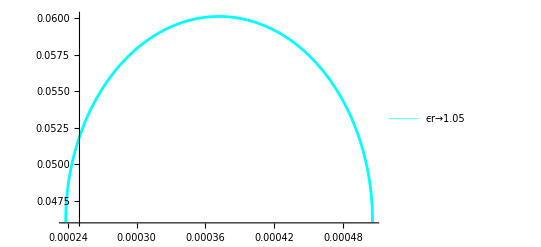

```mathematica
p1=Plot[q1/.ϵr->1.05,{Subscript[η, 0],η01p/.ϵr->1.05,η02p/.ϵr->1.05},PlotStyle->{Cyan,Cyan,Thickness[0.005]},PlotLegends->{"ϵr→1.05"}]
```

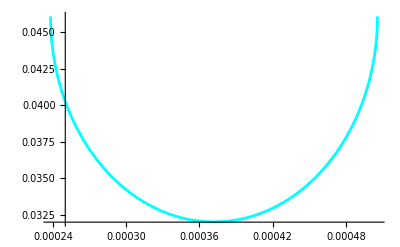

```mathematica
p12=Plot[q2/.ϵr->1.05,{Subscript[η, 0],η01p/.ϵr->1.05,η02p/.ϵr->1.05},PlotStyle->{Cyan,Cyan,Thickness[0.005]}]
```

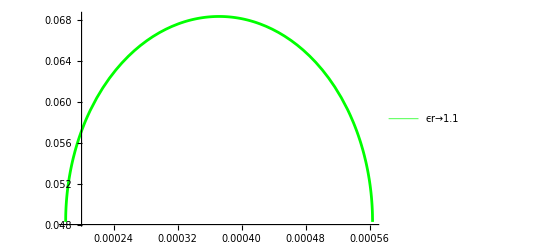

```mathematica
p2=Plot[q1/.ϵr->1.1,{Subscript[η, 0],η01p/.ϵr->1.1,η02p/.ϵr->1.1},PlotStyle->{Green,Green,Thickness[0.005]},PlotLegends->{"ϵr→1.1"}]
```

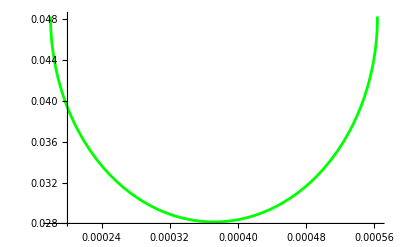

```mathematica
p22=Plot[q2/.ϵr->1.1,{Subscript[η, 0],η01p/.ϵr->1.1,η02p/.ϵr->1.1},PlotStyle->{Green,Green,Thickness[0.005]}]
```

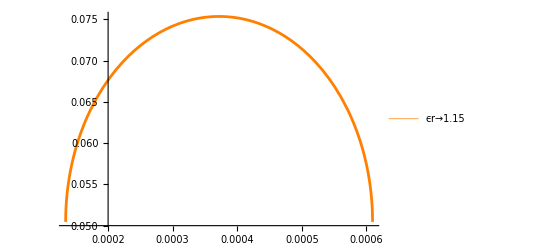

```mathematica
p4=Plot[q1/.ϵr->1.15,{Subscript[η, 0],η01p/.ϵr->1.15,η02p/.ϵr->1.15},PlotStyle->{Orange,Orange,Thickness[0.005]},PlotLegends->{"ϵr→1.15"}]
```

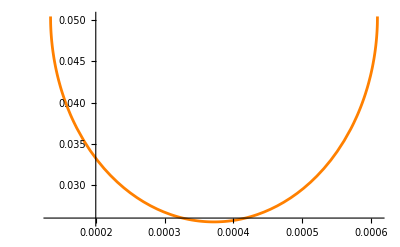

```mathematica
p42=Plot[q2/.ϵr->1.15,{Subscript[η, 0],η01p/.ϵr->1.15,η02p/.ϵr->1.15},PlotStyle->{Orange,Orange,Thickness[0.005]}]
```

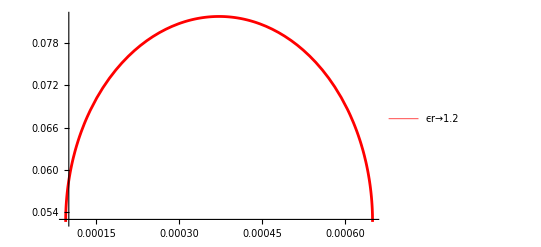

```mathematica
p5=Plot[q1/.ϵr->1.2,{Subscript[η, 0],η01p/.ϵr->1.2,η02p/.ϵr->1.2},PlotStyle->{Red,Red,Thickness[0.005]},PlotLegends->{"ϵr→1.2"}]
```

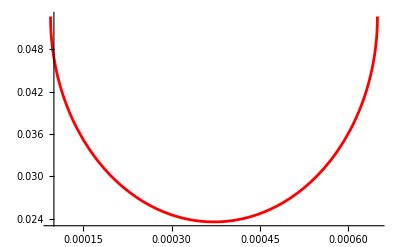

```mathematica
p52=Plot[q2/.ϵr->1.2,{Subscript[η, 0],η01p/.ϵr->1.2,η02p/.ϵr->1.2},PlotStyle->{Red,Red,Thickness[0.005]}]
```

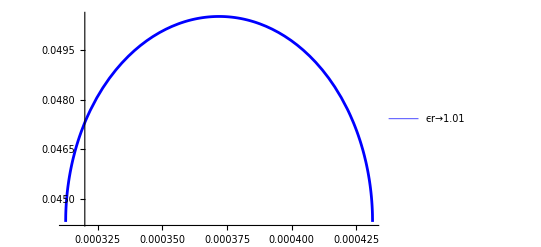

```mathematica
p3=Plot[q1/.ϵr->1.01,{Subscript[η, 0],η01p/.ϵr->1.01,η02p/.ϵr->1.01},PlotStyle->{Blue,Blue,Thickness[0.005]},PlotLegends->{"ϵr→1.01"}]
```

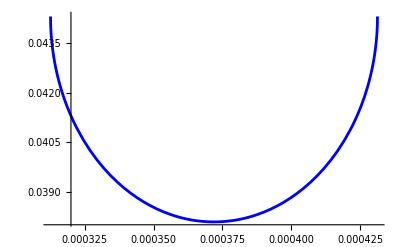

```mathematica
p32=Plot[q2/.ϵr->1.01,{Subscript[η, 0],η01p/.ϵr->1.01,η02p/.ϵr->1.01},PlotStyle->{Blue,Blue,Thickness[0.005]}]
```

```mathematica
hit=η02p/.ϵr->1
```

0.000371934

```mathematica
hitt=FullSimplify[q1]/.Subscript[η, 0]->hit/.ϵr->1
```

0.0438681

```mathematica
p6=Graphics[{PointSize[Large],Purple,Point[{hit,hitt}]}]
```

-Graphics-

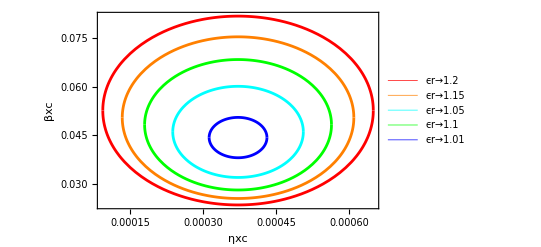

```mathematica
simpleplot=Show[p3,p32,p2,p22,p1,p12,p4,p42,p5,p52,PlotRange->Automatic,Frame->True,FrameLabel->{ηxc,βxc},FrameStyle->Directive[20],PlotRange->All]
```

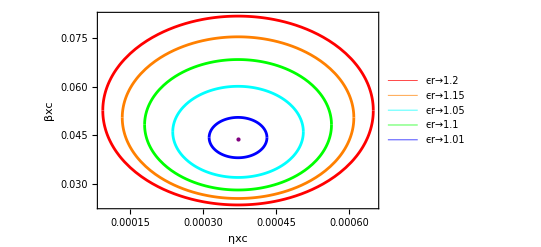

```mathematica
Show[simpleplot,p6,PlotRange->Automatic]
```

```mathematica
j=Simplify[Simplify[∫_0^L0 (1/ρ1)ⅆs+∫_L0^Ld (1/ρ2)ⅆs/.Ld->L0/λ/.L->1/λ/.r->1/ρ,{ρ>0,λ>0,L0>0}],{((ρ Re[1/(-1+ρ)]≥1||Re[1/(-1+ρ)]≤0)&&(Re[1/(-1+ρ)]<0||ρ Re[1/(-1+ρ)]>1||1/(-1+1/ρ)∉Reals))||1/(-1+ρ)∉Reals}]
```

-(L0 (λ-λ ρ+(-1+λ) ρ Log[ρ]))/(λ (-1+ρ) ρ0)

```mathematica
z=Simplify[Simplify[∫_0^L0 (∫_0^L0 (1/ρ1)ⅆs)ⅆs+∫_L0^Ld (∫_L0^Ld (1/ρ2)ⅆs)ⅆs/.Ld->L0/λ/.L->1/λ/.r->1/ρ,{ρ>0,λ>0,L0>0}],((ρ Re[1/(-1+ρ)]≥1||Re[1/(-1+ρ)]≤0)&&(Re[1/(-1+ρ)]<0||ρ Re[1/(-1+ρ)]>1||1/(-1+1/ρ)∉Reals))||1/(-1+ρ)∉Reals]
```

(L0 (L0+(L0 (-1+λ)^2 ρ Log[ρ])/(λ^2 (-1+ρ))))/ρ0

```mathematica
ph1=fq1/.ηss->0.0510/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q2/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->0.5/.s1->0.9/.s2->0.9/.Subscript[η, 0]->ηxcd/.ηxcd->0.0392248/.ϵr->2
```

0.9

```mathematica
k1=1/(ph1 l)/.l->0.2
```

7.59153

```mathematica
ph2=fq2/.ηss->0.0510/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q2/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->0.5/.s1->0.9/.s2->0.9/.Subscript[η, 0]->ηxcd/.ηxcd->0.0392248/.ϵr->2
```

-5.5268×10^-7

```mathematica
k2=1/(ph2 l)/.l->0.2
```

-6.97094

```mathematica
mpla11=f11/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q2/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->1.9/.s1->1/.s2->0.8;
mpla12=f11/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q1/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->1.9/.s1->1/.s2->0.8;
mpla21=f22/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q2/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->1.9/.s1->1/.s2->0.8;
mpla22=f22/.ηr->(Subscript[η, 0]/(-I3/2I4))/.βxcd->q1/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.θ̃->z/.θ->j/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s3->1.9/.s1->1/.s2->0.8;
```

```mathematica
h1=ParametricPlot[{mpla11/.ϵr->1.01,mpla21/.ϵr->1.01},{Subscript[η, 0],(η01p)/.ϵr->1.01,(η02p)/.ϵr->1.01},PlotStyle->{Blue,Blue,Thick},PlotLegends->{"ϵr→1.01"},LabelStyle->Directive[20]];
h2=ParametricPlot[{mpla12/.ϵr->1.01,mpla22/.ϵr->1.01},{Subscript[η, 0],(η01p)/.ϵr->1.01,(η02p)/.ϵr->1.01},PlotStyle->{Blue,Blue,Thick}];
Show[{h1,h2},PlotRange->Automatic]
```

-Graphics-

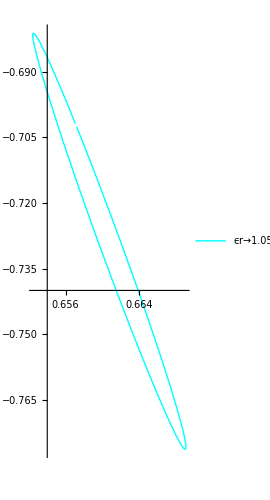

```mathematica
h3=ParametricPlot[{mpla11/.ϵr->1.05,mpla21/.ϵr->1.05},{Subscript[η, 0],(η01p)/.ϵr->1.05,(η02p)/.ϵr->1.05},PlotStyle->{Cyan,Cyan,Thick},PlotLegends->{"ϵr→1.05"},LabelStyle->Directive[20]];
h4=ParametricPlot[{mpla12/.ϵr->1.05,mpla22/.ϵr->1.05},{Subscript[η, 0],(η01p)/.ϵr->1.05,(η02p)/.ϵr->1.05},PlotStyle->{Cyan,Cyan,Thick}];
Show[{h3,h4},PlotRange->Automatic]
```

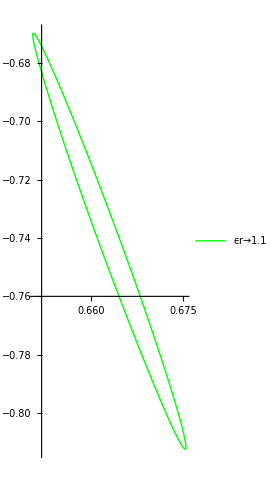

```mathematica
h5=ParametricPlot[{mpla11/.ϵr->1.1,mpla21/.ϵr->1.1},{Subscript[η, 0],(η01p)/.ϵr->1.1,(η02p)/.ϵr->1.1},PlotStyle->{Green,Green,Thick},PlotLegends->{"ϵr→1.1"},LabelStyle->Directive[20]];
h6=ParametricPlot[{mpla12/.ϵr->1.1,mpla22/.ϵr->1.1},{Subscript[η, 0],(η01p)/.ϵr->1.1,(η02p)/.ϵr->1.1},PlotStyle->{Green,Green,Thick}];
Show[{h5,h6},PlotRange->Automatic]
```

```mathematica
h7=ParametricPlot[{mpla11/.ϵr->1.15,mpla21/.ϵr->1.15},{Subscript[η, 0],(η01p)/.ϵr->1.15,(η02p)/.ϵr->1.15},PlotStyle->{Orange,Orange,Thick},PlotLegends->{"ϵr→1.15"},LabelStyle->Directive[20]];
h8=ParametricPlot[{mpla12/.ϵr->1.15,mpla22/.ϵr->1.15},{Subscript[η, 0],(η01p)/.ϵr->1.15,(η02p)/.ϵr->1.15},PlotStyle->{Orange,Orange,Thick}];
```

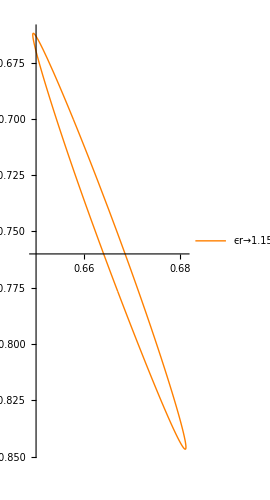

```mathematica
Show[{h7,h8},PlotRange->Automatic]
```

```mathematica
h9=ParametricPlot[{mpla11/.ϵr->1.2,mpla21/.ϵr->1.2},{Subscript[η, 0],(η01p)/.ϵr->1.2,(η02p)/.ϵr->1.2},PlotStyle->{Red,Red,Thick},PlotLegends->{"ϵr→1.2"},LabelStyle->Directive[20]];
h10=ParametricPlot[{mpla12/.ϵr->1.2,mpla22/.ϵr->1.2},{Subscript[η, 0],(η01p)/.ϵr->1.2,(η02p)/.ϵr->1.2},PlotStyle->{Red,Red,Thick}];
```

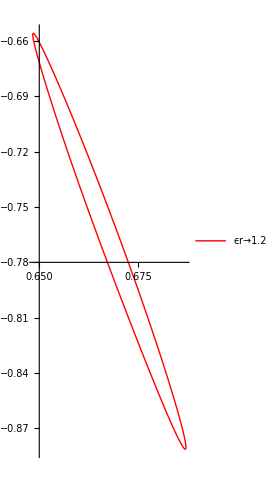

```mathematica
Show[{h9,h10},PlotRange->Automatic]
```

```mathematica
hh=Graphics[{PointSize[Large],Purple,Point[{ph1,ph2}]}]
```

-Graphics-

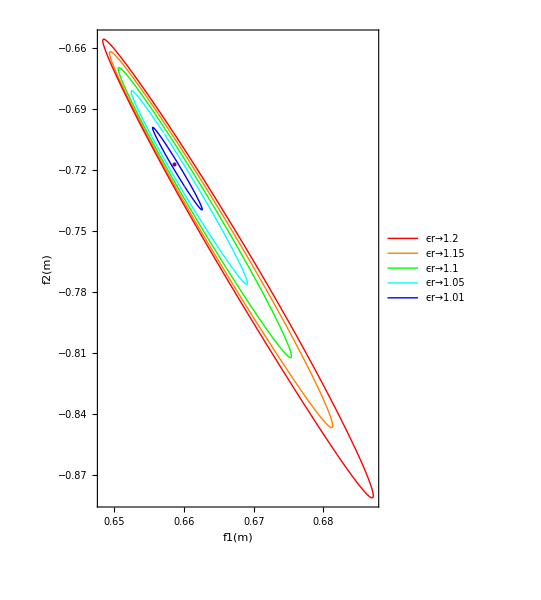

```mathematica
Show[{h1,h2,h3,h4,h5,h6,h7,h8,h9,h10,hh},Frame->True,AspectRatio->1.5,AxesLabel->{f1[m] ,f2[m]},FrameStyle->Directive[20],PlotRange->All]
```

## tme phase advance for the whole cell

```mathematica
AA=A/.θ̃->z/.θ->j/.I1->(L0^3 (4-(3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/(-1+r)^3))/(12 ρ0^5)/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->(L0^3 (-2-(3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/(-1+r)^3))/(6 ρ0^4)/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.ϵr->1/.Subscript[η, 0]->hit/.ηr->1/.βr->1
```

{0.837808,0.837808}

```mathematica
ASIN=(1-(AA)^2)^0.5
```

{0.545965,0.545965}

```mathematica
TAN=ASIN/AA
```

{0.65166,0.65166}

```mathematica
ArcTan[TAN]
```

{0.577541,0.577541}

```mathematica
(3Pi/2+ArcTan[TAN])(180/Pi)
```

{303.091,303.091}

```mathematica
Aforplot=A/.θ̃->z/.θ->j/.I1->(L0^3 (4-(3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/(-1+r)^3))/(12 ρ0^5)/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->(L0^3 (-2-(3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/(-1+r)^3))/(6 ρ0^4)/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.ρ0->5.4/.θt->(2π)/100
```

{((1.8844×10^-13 λ^6 ((«1»«1»)^6 «1» (2+(-1+«1»-(«1»)/(«1»))/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 («1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4+(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2))/((1.8844×10^-13 λ^6 ((«1»«1»)^6 «1» (2+(-1+«1»-(«1»)/(«1»))/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 («1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4-(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2)),((«1»)/(«1»)+«3»)/((«1»)/(«1»)+«4»)}

```mathematica
Aforplotabs=Aforplot/.ηr->1/.βr->1
```

{((1.8844×10^-13 λ^6 ((«1»«1»)^6 «1» (2+(-1+«1»-(«1»)/(«1»))/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 («1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4+(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2))/((1.8844×10^-13 λ^6 ((«1»«1»)^6 «1» (2+(-1+«1»-(«1»)/(«1»))/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 («1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4-(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2)),((«1»)/(«1»)+«3»)/((«1»)/(«1»)+«4»)}

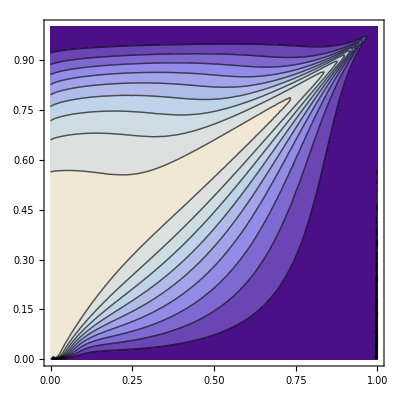

```mathematica
ContourPlot[Aforplotabs,{ρ,0,1},{λ,0,1}]
```

```mathematica
ASINplot=(1-(Aforplotabs)^2)^0.5
```

{(1-(((«24» «4» (4-«1»))/(«1»)^6+«2»+(«1»)/(«5»«1»«1»))^2)/(((«24» «4» (4-«1»))/(«1»)^6+«4»)^2))^0.5,(1-(«1»)^2/(«1»)^2)^0.5}

```mathematica
ContourPlot[ASINplot,{ρ,0,1},{λ,0,1}]
```

-Graphics-

```mathematica
TANplot=ASINplot/Aforplotabs
```

{(((1.8844×10^-13 λ^6 («1»)^6 ((«1»«1»)^2 (2+(«1»)/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 ((«1»«1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4-(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2)) ((«1»«1»)^0.5)/((1.8844×10^-13 λ^6 ((«1»«1»)^6 «1» (2+(-1+«1»-(«1»)/(«1»))/(-1+1/ρ)) (4-(«1»)/((-1+«1»)^3 («1»)^2)))/(λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])^6+(«1»)/(«1»)^5+(«1»)/(«1»)^4+(π^2 ((«1»«1»)^2 ((«1»)/(«1»)^6-(«1»)/(«1»)^6))/(10000 («5»+«1»)^2)),((«1») «1»)/(«1»)}

moires tis phase advance se sxesi me R,dld me logo aktinwn kampulotitas.

```mathematica
ContourPlot[(3Pi/2+ArcTan[TANplot])(180/Pi),{ρ,0,1},{λ,0,1},Contours->20,ColorFunction->ColorData["Rainbow"],PlotLegends->BarLegend[Automatic,LegendLabel->"μx[degrees °]"],FrameLabel->{"ρ","λ"},LabelStyle->Directive[20],PlotPoints->100]
```

-Graphics-

```mathematica
B={Subscript[cosϕy, TME],cosϕyr}={cosϕy/.{f1->fq1,f2->fq2}/.ηss->ηs2/.{ηxcd->ηr ηmin,βxcd->βr βmin}/.{ηmin->-I3/2I4,βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)}/.{ηr->1,βr->1},cosϕy/.{f1->fq1,f2->fq2}/.ηss->ηs2/.{ηxcd->ηr ηmin,βxcd->βr βmin}/.{ηmin->-I3/2I4,βmin->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)}}
```

{((-s2+(√(«1»))/(«1»))^2 «2» ((s2-(2 s2 s3 (-(I3 I4)/2+s1 θ+θ̃))/((-s2+(√(«1»+«1»+«1»))/(√((«1»)/4+«3»))) («1»))+(s2 (-(I3 I4)/2+s1 θ+θ̃))/(-(I3 I4)/2+s1 θ+s2 θ+θ̃-(2 s3 (-(I3 I4)/2+s1 θ+θ̃))/(-s2+(√(«1»))/(√(«1»))))) («1»)+((Ld+s1) (s2-«1»)+«1») «1»))/(4 s2^4 s3^2 (-(I3 I4)/2+s1 θ+θ̃)^4),((-s2+(«1»)/(√(«1»+«3»)))^2 «3»)/(4 s2^4 s3^2 (-1/2 I3 I4 ηr+s1 θ+θ̃)^4)}

```mathematica
{BB1,BB2}=Simplify[B/.θ̃->z/.θ->j/.I1->(L0^3 (4-(3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/(-1+r)^3))/(12 ρ0^5)/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->(L0^3 (-2-(3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/(-1+r)^3))/(6 ρ0^4)/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.274/.ρ->0.2/.ρ0->5.4/.θt->(2π)/100/.s1->1/.s2->0.8/.s3->1.9/.ϵr->1/.Subscript[η, 0]->hit/.ηr->1/.βr->1]
```

{0.0588706,0.0588706}

```mathematica
Reduce[BB1>-1&&BB1<1&&s3>0,s3]
```

s3>0

### sumfwna me tis times pou dothikan gia ta L0,Ld,ρ0 kai ρd prokuptei o arithmos twn dipolwn pou xrisimopoiountai:

```mathematica
theta=2j/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.1/.ρ->0.31/.ρ0->5.4/.θt->(2π)/100;
Ndip=Round[(2ℼ/theta)/.ℼ->3.14159265359]
```

100

```mathematica
s1=(π λ (-1+ρ) ρ1)/(100 (-λ+λ ρ+ρ Log[ρ]))/.λ->0.1/.ρ->0.31/.ρ1->5.4/.θt->(2π)/100
```

0.0270921

```mathematica
s2=Ld-(π λ (-1+ρ) ρ1)/(100 (-λ+λ ρ+ρ Log[ρ]))/.Ld->0.3/.λ->0.1/.ρ->0.31/.ρ1->5.4/.θt->(2π)/100
```

0.272908

```mathematica
s1+s2
```

0.3

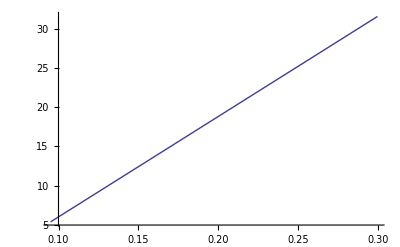

```mathematica
shape1=Plot[(1+((-1+r) (-1+s/L0))/(-1+L)) ρ0/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100,{s,s1,s2},PlotStyle->Thick]
```

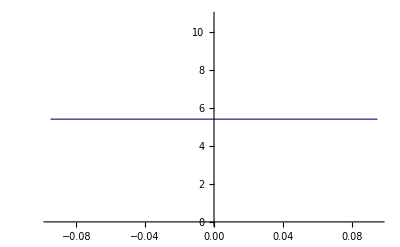

```mathematica
shape2=Plot[ρ0/.ρ0->5.4,{s,-s1,s1},PlotStyle->Thick]
```

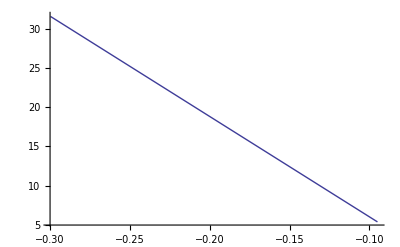

```mathematica
shape3=Plot[(1+((-1+r) (-1-s/L0))/(-1+L)) ρ0/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100,{s,-s1,-s2},PlotStyle->Thick]
```

```mathematica
Show[{shape3,shape2,shape1},Frame->True,FrameLabel->{s[m] ,bending radius ρ[m]},FrameStyle->Directive[20],PlotRange->Automatic]
```

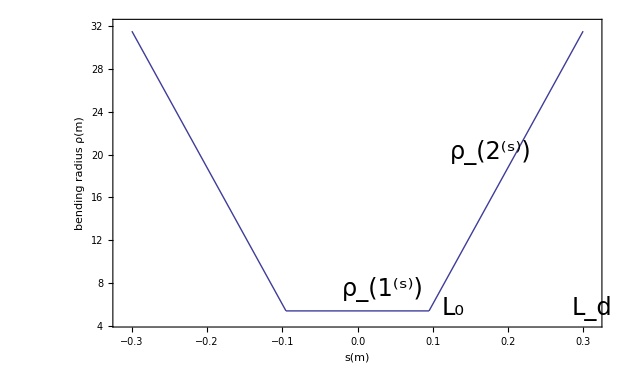

```mathematica
Bmax=2.86/(0.299796139*ρ0)/.ρ0->5.4
```

1.76663

```mathematica
Subscript[ρ, 1^(s)]
```

```mathematica
BB=Bmax/(((-Ld+L1 r+s-r s) ρ1)/(L1-Ld))/.L1->Ld/(1+1/λ)/.Ld->0.3/.r->1/ρ/.λ->0.1/.ρ->0.31/.ρ1->5.4/.θt->(2π)/100
```

-0.0892239/(-0.212023-2.22581 s)

```mathematica
2.86/(0.299796139(((-Ld+L1 r+s-r s) ρ1)/(L1-Ld)))/.L1->Ld/(1+1/λ)/.Ld->0.3/.r->1/ρ/.λ->0.1/.ρ->0.31/.ρ1->5.4/.θt->(2π)/100
```

-0.481809/(-0.212023-2.22581 s)

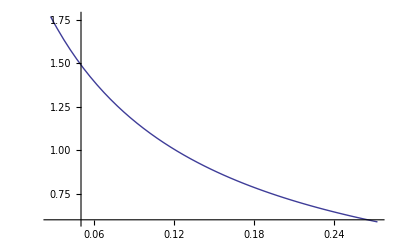

```mathematica
shape11=Plot[%,{s,s1,s2},PlotStyle->Thick]
```

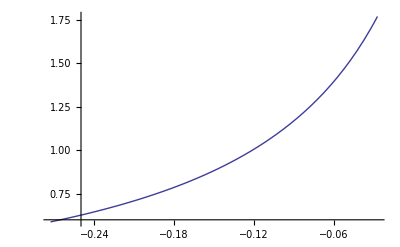

```mathematica
shape22=Plot[-0.48180888828739854/(-0.21202346041055717+2.2258064516129035 s),{s,-s1,-s2},PlotStyle->Thick]
```

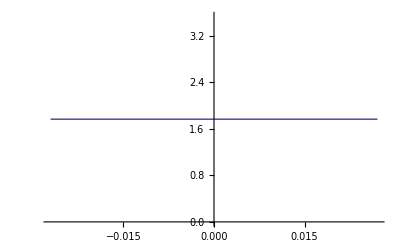

```mathematica
shape33=Plot[Bmax,{s,-s1,s1},PlotStyle->Thick]
```

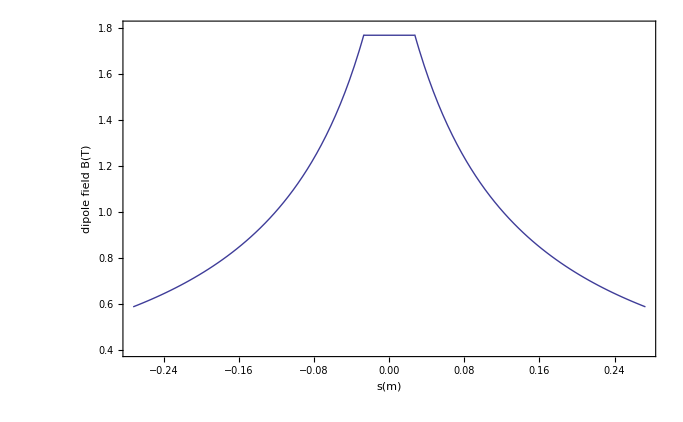

```mathematica
Show[{shape33,shape22,shape11},Frame->True,FrameLabel->{s[m] ,dipole field B[T]},FrameStyle->Directive[20],PlotRange->{0.4,1.8}]
```

```mathematica
-0.48180888828739854/(-0.21202346041055717-2.2258064516129035 s)/.s->s1
```

1.76924

```mathematica
-0.48180888828739854/(-0.21202346041055717-2.2258064516129035 s)/.s->s2
```

0.587956

```mathematica
s1
```

0.0270921

```mathematica
s2
```

0.272908

```mathematica
0.0271+0.273
```

0.3001

## emittance geom.

```mathematica
G=(Cq*γ^2/(Subscript[J, x](∫_0^L0 (1/ρ1^2)ⅆs+∫_L0^Ld (1/ρ2^2)ⅆs)))/.Cq->3.84*10^-13/.γ->5597/.Subscript[J, x]->1/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

0.00269696

```mathematica
FullSimplify[(Cq*γ^2/(Subscript[J, x](∫_0^L0 (1/ρ1^2)ⅆs+∫_L0^Ld (1/ρ2^2)ⅆs)))/.Cq->3.84*10^-13/.γ->5597/.Subscript[J, x]->1/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))]
```

ConditionalExpression[(0.0000240587 ρ0 (λ-1. λ ρ+(-1.+λ) ρ Log[ρ]))/(θt (λ (-1.+ρ)-1. ρ) (-1.+ρ)),Re[ρ/(-1+ρ)]>1||(1/(-1+1/ρ)∉Reals&&(Re[ρ/(-1+ρ)]≤0||Re[ρ/(-1+ρ)]≥1))||Re[ρ/(-1+ρ)]<0||ρ/(-1+ρ)∉Reals]

```mathematica
Subscript[ϵ, TME]=FullSimplify[Subscript[ϵ, xNEW]/.Subscript[β, 0]->(√(-I3^2+4 I2 I4))/(2 √I1 √I4)/.Subscript[η, 0]->-I3/(2 I4)]/.I1->1/(12 ρ0^5)L0^3 (4-1/(-1+r)^3 3 (-1+L)^5 L0^2 ((-1-2 Log[(-1+L) L0] (1+Log[(-1+L) L0]))/((-1+L)^2 L0^2)+(1+2 Log[L L0+Ld (-1+r)-L0 r] (1+Log[L L0+Ld (-1+r)-L0 r]))/(L L0+Ld (-1+r)-L0 r)^2))/.I2->1/(20 ρ0^5)L0^5 (1-1/(-1+r)^5 5 (-1+L)^5 (1/(-1+L)^2((L-r) (-16+11 L+5 r)+2 Log[(-1+L) L0] (2+3 L^2+2 L (-4+r)+(4-3 r) r-(L-r)^2 Log[(-1+L) L0]))-1/(-L L0+Ld+L0 r-Ld r)^2(L0 (L-r) (11 L L0+16 Ld (-1+r)-11 L0 r)+2 Log[L L0+Ld (-1+r)-L0 r] (3 L^2 L0^2+2 Ld^2 (-1+r)^2-8 L0 Ld (-1+r) r+3 L0^2 r^2-2 L L0 (-4 Ld (-1+r)+3 L0 r)-L0^2 (L-r)^2 Log[L L0+Ld (-1+r)-L0 r]))))/.I3->1/(6 ρ0^4)L0^3 (-2-1/(-1+r)^3 3 (-1+L)^4 L0 ((-4+L+3 r+2 (-L+r) Log[(-1+L) L0])/((-1+L)^2 L0)+(-L L0+4 Ld+L0 r-4 Ld r+2 L0 (L-r) Log[L L0+Ld (-1+r)-L0 r])/(-L L0+Ld+L0 r-Ld r)^2))/.I4->(L0 (2+(-1+L-((-1+L)^3 L0^2)/(-L L0+Ld+L0 r-Ld r)^2)/(-1+r)))/(2 ρ0^3)/.Cq->3.84*10^-13/.γ->5597/.Subscript[J, x]->1/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.λ->0.31703118/.ρ->0.171238/.ρ0->5.4/.θt->(2π)/100
```

1.21163×10^-11

```mathematica
Enorma=Subscript[ϵ, TME]*γ/.γ->5597
```

6.78151×10^-8

for uniform of the same bending angle thi=j:

```mathematica
thi=(2π)/100
```

π/50

```mathematica
emit=(1/(12(15)^0.5))(Cq*γ^2(thi)^3)/.Cq->3.84*10^-13/.γ->5597
```

6.42029×10^-11

```mathematica
e=emit*γ/.γ->5597
```

3.59344×10^-7

```mathematica
e/Enorma
```

5.29887

## momentum compaction function

```mathematica
ηsxtme1=Simplify[η0+∫_0^L0 (∫_0^L0 (1/ρ1)ⅆs)ⅆs/.η0->η01p]
```

0.000319369-0.000305099 √(-1+ϵr^2)+L0^2/ρ0

```mathematica
ηsxtme2=Simplify[Simplify[ηsxtme1+∫_L0^Ld (∫_L0^Ld (1/ρ2)ⅆs)ⅆs/.η0->η01p,{ρ>0,Ld>L0,ρ<1,λ>0,ρ0>0,λ<1,L0>0,Ld>0}],{(L0>Ld+L0 Re[(-1+L)/(-1+r)]||Re[(-1+L)/(-1+r)]>0||((L0≥Ld+L0 Re[(-1+L)/(-1+r)]||Re[(-1+L)/(-1+r)]≥0)&&(L0-L L0)/(-1+r)∉Reals)||(-1+L)/(-1+r)∉Reals)&&(Ld+(L0 Im[L])/Im[r]≤L0||(Im[r]≥0&&(Im[L]≥0||Im[r]+Im[L] Re[r]≤Im[L]+Im[r] Re[L]))||(Im[r]≤0&&(Im[L]≤0||Im[r]+Im[L] Re[r]≥Im[L]+Im[r] Re[L])))}]
```

0.000319369-0.000305099 √(-1+ϵr^2)+L0^2/ρ0+((-1+L) L0 (L0-Ld) (Log[(-1+L) L0]-Log[L L0+Ld (-1+r)-L0 r]))/((-1+r) ρ0)

```mathematica
ηsxtme1abs=ηsxtme1/.ϵr->1
```

0.000319369+L0^2/ρ0

```mathematica
ηsxtme2abs=ηsxtme2/.ϵr->1
```

0.000319369+L0^2/ρ0+((-1+L) L0 (L0-Ld) (Log[(-1+L) L0]-Log[L L0+Ld (-1+r)-L0 r]))/((-1+r) ρ0)

```mathematica
αgeneral=Simplify[(1/Ld)((∫_0^L0 (ηsxtme1/ρ1)ⅆs)+(∫_L0^Ld (ηsxtme2/ρ2)ⅆs))/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ])),{ρ>0,Ld>L0,ρ<1,λ>0,ρ0>0,λ<1}]
```

-1/(4 ρ0)λ (-0.00127748+0.0012204 √(-1+ϵr^2)-(θt^2 λ^2 (-1+ρ)^2 ρ0)/(λ-λ ρ+(-1+λ) ρ Log[ρ])^2+1/(-1+1/ρ)(-1+1/λ) Log[ρ] (0.00127748-0.0012204 √(-1+ϵr^2)+(θt^2 λ^2 (-1+ρ)^2 ρ0)/(λ-λ ρ+(-1+λ) ρ Log[ρ])^2+(θt^2 (-1+λ)^2 (-1+ρ) ρ ρ0 Log[ρ])/(λ-λ ρ+(-1+λ) ρ Log[ρ])^2))

```mathematica
αabs=Simplify[(1/Ld)((∫_0^L0 (ηsxtme1abs/ρ1)ⅆs)+(∫_L0^Ld (ηsxtme2abs/ρ2)ⅆs))/.Ld->(L0/λ)/.L->1/λ/.r->1/ρ/.L0->-(θt λ (-1+ρ) ρ0)/(2 (λ-λ ρ-ρ Log[ρ]+λ ρ Log[ρ]))/.ρ0->5.4/.λ->0.31703118/.ρ->0.171238/.θt->(2π)/100]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

0.000339179